In order to create an autonomous file, we need to study all the maximum on f(t) as half maximum, this means considering them as interior points or maximum at the exterior. One needs to use the Corollary 12.1.2  that arises from the study of the endpoints as f’(t)=0, we need to calculate the second derivative.

```mathematica
Clear[F1,F2,u,f5]
```

```mathematica
u[x_,t_]:=Exp[x*Cos[t]]
```

```mathematica
f5[x_]:=Integrate[u[x,t],{t,0,2*Pi}]/(Exp[x]*Sqrt[2])
```

We introduce the ceiling and floor function to create a sum which counts the total number of maximums on a given domain. We treat every maxima as a half maximum continuing with Corollary 12.1.2

```mathematica
F1[x_]:=Ceiling[x/(2*Pi)]
```

```mathematica
F2[x_]:=Floor[x/(2*Pi)]
```

```mathematica
Table[F1[x]+F2[x],{x,Pi,8*Pi,Pi/2}]
```

{1,1,2,3,3,3,4,5,5,5,6,7,7,7,8}

```mathematica
F3[x_]:=(F1[x]+F2[x])*Exp[x]*Sqrt[Pi/(2*x)]
```

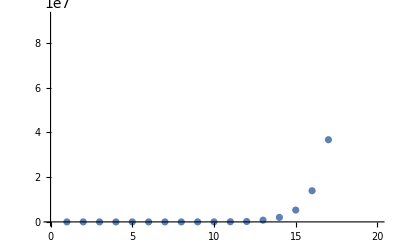

```mathematica
ListPlot[Table[F3[x],{x,1,20}]]
```

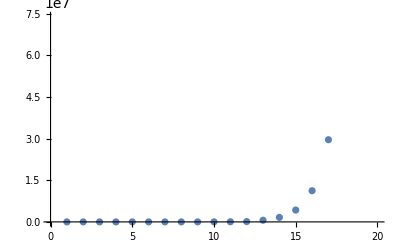

```mathematica
ListPlot[Table[Integrate[Exp[x*Cos[t]],{t,Pi,x}],{x,1,20}]]
```

Comparison between the laplace approximation and the numerical exact solution on an interval of t=[Pi,3Pi] for different values of x. Due to Wolfram numerical limitations the magnitude of x should not increase too much.

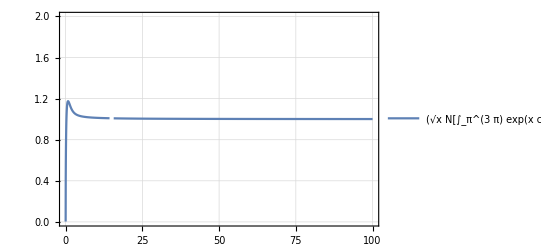

```mathematica
Plot[(Sqrt[x]*N[Integrate[Exp[x*Cos[t]],{t,Pi,3Pi}]])/(Exp[x]*Sqrt[2*Pi]),{x,0,100},PlotTheme->"Detailed",PlotRange->{0,2}]
```